See Godf2002, Cardinality Estimation ...

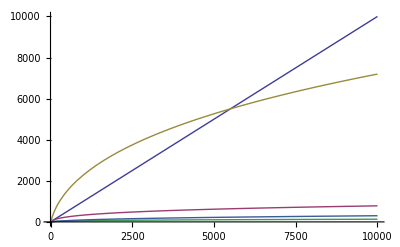

```mathematica
sc[n_, d_] := Log[n]^(d-1)
scr[n_, d_]:= Log[n]^(d-1)/((d-1)!)

Plot[Tooltip[{ n , sc[n,4], sc[n,5], scr[n,4], scr[n,5]}], {n, 1, 10000}]
```